## Extraction of the Regge poles

The extraction of the Regge poles has been done by hands, the summary is in my internship report. Therefore I start straight the computations of the Regge poles from equation 3.18 (pol = p_k(s)) :

```mathematica
kmax:=100;
Clear[k, d, s, pol];
P = ParallelTable[1/(n!)NorlundB[n, s+1, s+1]//Simplify,{n, 0, kmax}];
pol = ParallelTable[
2^(2k)∑_(n1=0)^k (-s)^n1(∑_(m=0)^Floor[n1/2 ] Pochhammer[s+(d-1)/2+m-k, Floor[k/2]-m]/(m!(n1-2m)!2^(2m+n1)))P[[k-n1+1]]//Simplify,
{k, 0, kmax},
Method->"FinestGrained"
]
```

In order to get the polynomes without recomputing everything:

```mathematica
kmax = 100;
pol =
```

To arrive to the integral expression of section 4.1, a resumation was necessary. This was done like this (p = Floor(k/2)) :

```mathematica
∑_(n=0)^p Pochhammer[s+(d-1)/2+n , p-n]/(2^(4n)n!)((s+2p) t)^(2n)//FullSimplify
```

Gamma[-1/2+d/2+p+s] Hypergeometric0F1Regularized[1/2 (-1+d)+s,1/16 (2 p+s)^2 t^2]-(16^-p ((2 p+s) t)^(2 p) (-1+HypergeometricPFQ[{1},{1+p,-1/2+d/2+p+s},1/16 (2 p+s)^2 t^2]))/Gamma[1+p]

Only the first term will give a non zero value in the integral I have to compute explaining why I only kept this one. I then do a quick check that the integral expression is exact  by plotting for various value of s and d the plot in k:

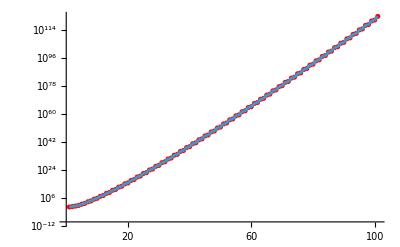

```mathematica
dd = 5;
ss = 0;
intVal = Table[((-1)^k 2^(2k)Gamma[ss+(dd-1)/2])/(k!√Pi Gamma[ss+(dd-2)/2])Pochhammer[ss+(dd-1)/2, Floor[k/2]]NIntegrate[(1-u^2)^(ss+(dd-4)/2)NorlundB[k, ss+k+1, ((ss+k)/2)(1-u)], {u, -1,1}],{k, 0, kmax}];
polVal = Table[pol[[kk+1]]/.d->dd/.s->ss+kk,{kk, 0, kmax}];

Show[
ListPlot[polVal, ScalingFunctions->{"Linear","Log"}, PlotStyle->Red],
ListLinePlot[intVal, ScalingFunctions->{"Linear","Log"}]
]
```

## Asymptotic of p_k(s+k)

The first graph I want to take a look at is p_k(k) in function of d.

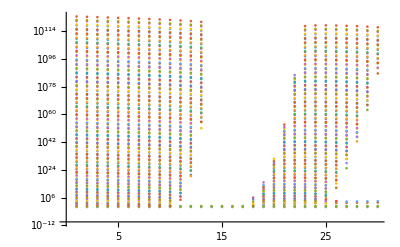

```mathematica
Clear[dd, kk];
polkD = Table[pol[[kk+1]]/.d->dd/.s->kk,{kk, 0, kmax}, {dd, 1, 30}];
ListPlot[
polkD 
,ScalingFunctions->{"Linear","Log"}]
```

From this graph, two things are clear, after d = 10, the positivity isn’t verified. Also, for large k, the positivity might not depend to much on the dimension. However, the very steep slope of the first limit of points may imply a very slow convergence of an approximation where d can be neglected. The asymptotic may still be interesting and the expression we got in section 4.2 is numerically quite good :

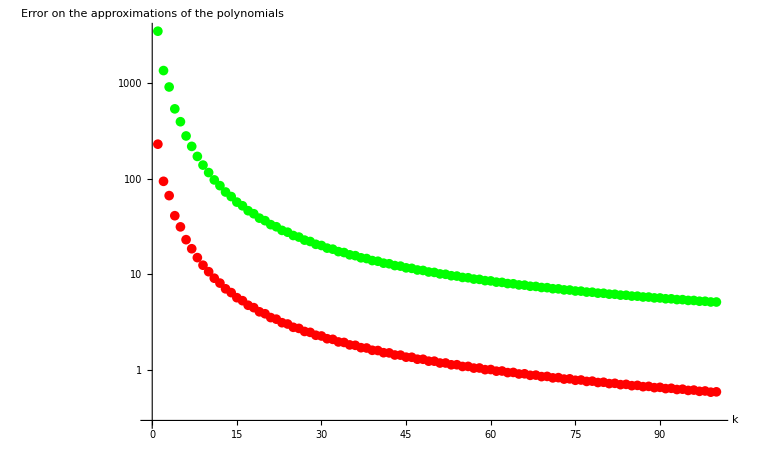

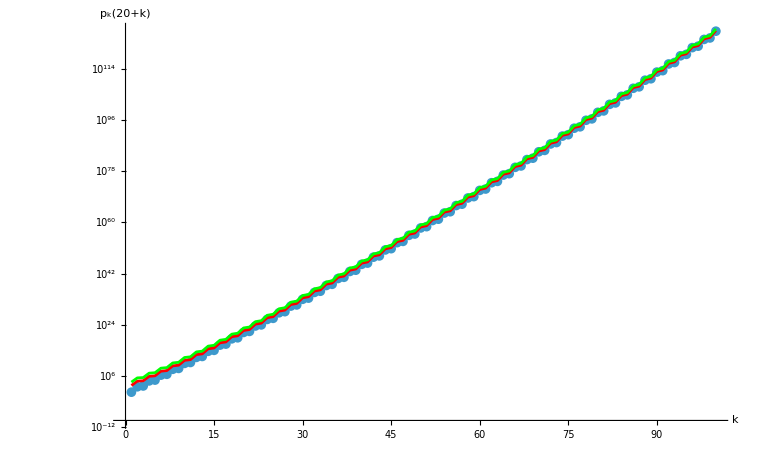

```mathematica
Clear[s, ss, dd];
polK = Table[pol[[k+1]]/.s->s+k,{k,1,100}];
ss=20;
dd=10;
approx1 = Table[((-1)^(ss+k+(dd-2)/2)2^(2(ss+k)+dd-3))/(√Pi)Gamma[ss+(dd-1)/2+Floor[k/2]]/(k+ss)^(ss+(dd-2)/2)NorlundB[ss+k+(dd-2)/2,ss+k+1,0]/((ss+k+(dd-2)/2)!),{k, 1, 100}];
approx2 = Table[2^(2(ss+k)+dd-3)/(√Pi)Gamma[ss+(dd-1)/2+Floor[k/2]]/(k+ss)^(ss+(dd-2)/2)(Log[ss+k+dd/2-1])^((-(dd-2))/2),{k, 1, 100}];
valPol = Evaluate[polK/.s->ss/.d->dd];
approx1/valPol//N;
approx2/valPol//N;
ListPlot[{Abs[%%-1],Abs[%-1]}, ScalingFunctions->"Log", PlotStyle->{Red, Green}, AxesLabel->{"k", "Error on the approximations of the polynomials"}]
Show[
ListPlot[valPol,ScalingFunctions->"Log", AxesLabel->{"k", "p_k(20+k)"}],
ListLinePlot[approx1, ScalingFunctions->"Log", PlotStyle->Red],
ListLinePlot[approx2, ScalingFunctions->"Log", PlotStyle->Green]
]
```